```mathematica
Get["/home/saul/Documents/Wolfram/QMB.wl"];
Get["/home/saul/Documents/Wolfram/MatrixComponent.wl"];
```

```mathematica
SFF[energies_,t_]:=Abs[Total[Exp[-I*energies*t]]]^2;

GOESFF[t_]:=If[t<1,2t-t*Log[1+2*t],2-t*Log[(2t+1)/(2t-1)]];
(*Retorna una lista de {x,y}*)
AverageWindow[data_,bins_]:=Module[{B=Partition[data,bins]},
Table[{Mean[First/@ B[[i]]],Mean[Last/@B[[i]]]},{i,Length[B]}]];
```

```mathematica
(*Parametros*)
n=8;
tH=2.Pi;
f=1/100; (*Step inicial*)
rate=70.;
tmax=5.;
J=1;
U=10;
```

```mathematica
(*Simetrico*)
Energies=Sort[Normal[SymmetricSectorHamiltonian[n,n,J,U,"Symmetric"]]//Eigenvalues];
UnfoldEnergies=Unfold[Energies]["UnfoldedLevels"];

(*AntiSimetrico*)
EnergiesAnti=Sort[Normal[SymmetricSectorHamiltonian[n,n,1,1,"Antisymmetric"]]//Eigenvalues];
UnfoldEnergiesAnti=Unfold[EnergiesAnti]["UnfoldedLevels"];
```

```mathematica
SFFData=Table[{t,SFF[UnfoldEnergies,tH*t]/Length[UnfoldEnergies]},{t,f,tmax,f/rate}];
SFFDataAnti=Table[{t,SFF[UnfoldEnergiesAnti,tH*t]/Length[UnfoldEnergiesAnti]},{t,f,tmax,f/rate}];
```

Suavizado por ventanas de tiempo:

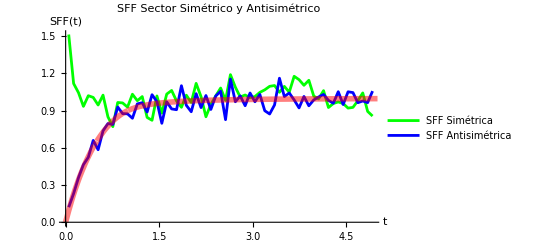

```mathematica
bin=550;
SmoothSFFData=AverageWindow[SFFData,bin];
SmoothSFFDataAnti=AverageWindow[SFFDataAnti,bin];
Show[ListPlot[{SmoothSFFData,SmoothSFFDataAnti},Joined->True,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotStyle->{Green,Blue},PlotLabel->"SFF Sector Simétrico y Antisimétrico",PlotLegends->{"SFF Simétrica","SFF Antisimétrica"}],
Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]]
```

Promediado entre sectores:

```mathematica
SectorAverage=Table[{SFFData[[t,1]],Mean[{SFFData[[t,2]],SFFDataAnti[[t,2]]}]},{t,Length[SFFData]}];
```

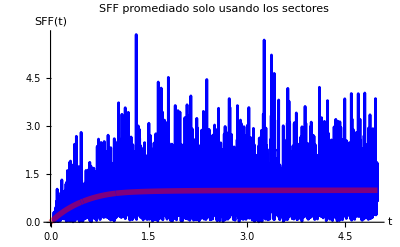

```mathematica
Show[{ListPlot[SectorAverage,Joined->True,PlotStyle->Blue,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotLabel->"SFF promediado solo usando los sectores"],Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]}]
```

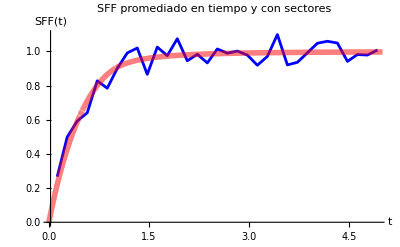

```mathematica
WindowSectorAverage=AverageWindow[SectorAverage,bin];
Show[{ListPlot[WindowSectorAverage,Joined->True,PlotStyle->Blue,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotLabel->"SFF promediado en tiempo y con sectores"],Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]}]
```

Comparación de Resultados: Usando el mismo tamaño de “bin”

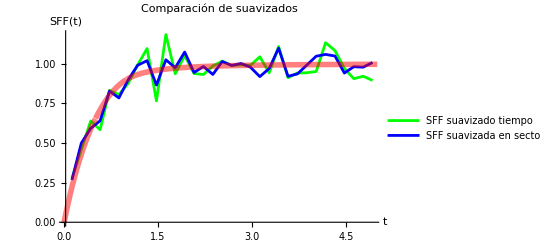

```mathematica
Show[{ListPlot[{SmoothSFFData,WindowSectorAverage},Joined->True,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotStyle->{Green,Blue},PlotLabel->"Comparación de suavizados",PlotLegends->{"SFF suavizado tiempo","SFF suavizada en sectores y tiempo"}],
Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]}]
```

```mathematica
GlobalEnergies= Sort[Normal[DeepHamiltonianBH[n,n,J,U]]//Eigenvalues];
UnfloldGlobal=Unfold[GlobalEnergies]["UnfoldedLevels"];
```

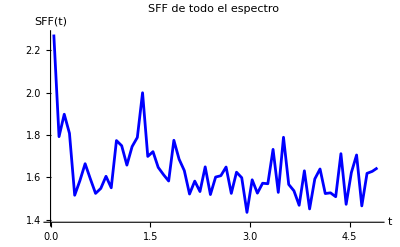

```mathematica
SFFGlobal=Table[{t,SFF[UnfloldGlobal,tH*t]/Length[UnfloldGlobal]},{t,f,tmax,f/rate}];
SmoothSFFGlobal=AverageWindow[SFFGlobal,bin];

Show[{ListPlot[SmoothSFFGlobal,Joined->True,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotStyle->Blue,PlotLabel->"SFF de todo el espectro"],
Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]}]
```

Comparando todo el espectro vs un sector particular

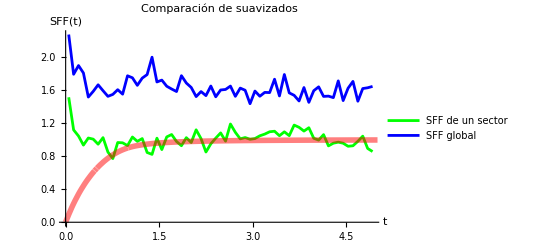

```mathematica
Show[{ListPlot[{SmoothSFFData,SmoothSFFGlobal},Joined->True,AxesLabel->{"t","SFF(t)"},PlotRange->All,PlotStyle->{Green,Blue},PlotLabel->"Comparación de suavizados",PlotLegends->{"SFF de un sector","SFF global"}],
Plot[GOESFF[t],{t,0,tmax},PlotStyle->Directive[Red,Thickness[0.01],Opacity[0.5]],PlotRange->All]}]
```